# Centerpos

```mathematica
l[a_,b_,c_,d_,e_,f_,g_,h_]:=h+Sum[x,{x,18-e-f-g,18-e-f}]+Sum[Sum[y,{y,0,x}]+1,{x,18-e-f,18-e}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,18-e,18}]-1350+4845*(d+Sum[x,{x,22-a-b-c,22-a-b}]+Sum[Sum[y,{y,0,x}]+1,{x,22-a-b,22-a}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,22-a,22}]-2324)
```

```mathematica
l[0,0,0,1,0,0,0,0]
```

4846

```mathematica
23!/16!/24
```

51482970

```mathematica
m[a_,b_,c_,d_,e_,f_,g_,h_]:=h+Sum[x,{x,i-e-f-g,i-e-f}]+Sum[Sum[y,{y,0,x}]+1,{x,i-e-f,i-e}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,i-e,i}]-k+4846*(d+Sum[x,{x,j-a-b-c,j-a-b}]+Sum[Sum[y,{y,0,x}]+1,{x,j-a-b,j-a}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,j-a,j}]-l)
```

```mathematica
tmp=Simplify[l[a,b,c,d,e,f,g,h]]
```

4842-1615/8 (-90 a^3+a^4+a^2 (3035-12 b)-6 a (7575-88 b+2 b^2-4 c)-4 (-66 b^2+b^3+b (1451-6 c)+129 c-3 c^2+6 d))-1/24 (-17+e) (-7104+1094 e-57 e^2+e^3)+1/6 (1+f) (1032+3 e^2+3 e (-37+f)-55 f+f^2)-1/2 (1+g) (-36+2 e+2 f+g)+h

```mathematica
(*Simplify[l[a,b,c,d,e,f,g,h],ComplexityFunction->t]*)
```

```mathematica
FactorTerms[tmp]
```

1/24 (220205250 a-14704575 a^2+436050 a^3-4845 a^4+28120380 b-2558160 a b+58140 a^2 b-1279080 b^2+58140 a b^2+19380 b^3+2500020 c-116280 a c-116280 b c-58140 c^2+116280 d+25234 e-2051 e^2+74 e^3-e^4+3884 f-432 e f+12 e^2 f-216 f^2+12 e f^2+4 f^3+420 g-24 e g-24 f g-12 g^2+24 h)

```mathematica
HornerForm[24*tmp]
```

b (28120380+b (-1279080+19380 b)-116280 c)+a (220205250+b (-2558160+58140 b)+a (-14704575+(436050-4845 a) a+58140 b)-116280 c)+(2500020-58140 c) c+116280 d+f (3884+f (-216+4 f)-24 g)+e (25234+f (-432+12 f)+e (-2051+(74-e) e+12 f)-24 g)+(420-12 g) g+24 h

```mathematica
CForm[%]
```

b*(28120380 + b*(-1279080 + 19380*b) - 116280*c) + 
   a*(220205250 + b*(-2558160 + 58140*b) + a*(-14704575 + (436050 - 4845*a)*a + 58140*b) - 116280*c) + 
   (2500020 - 58140*c)*c + 116280*d + f*(3884 + f*(-216 + 4*f) - 24*g) + 
   e*(25234 + f*(-432 + 12*f) + e*(-2051 + (74 - e)*e + 12*f) - 24*g) + (420 - 12*g)*g + 24*h

```mathematica
t[x_]:=Tr@((Length[#]-1)&/@(Extract[x,{Sequence@@Drop[#,-1]}]&/@Position[x,Times]))
```

```mathematica
$RecursionLimit=Infinity
```

∞

```mathematica
Clear[trial];trial[a_,b_,c_,d_,e_,f_,g_,h_]:=trial[a,b,c,d,e,f,g,h]=If[h==0,If[g==0,If[f==0,If[e==0,If[d==0,If[c==0,If[b==0,If[a==0,0,trial[a-1,21-a,c,d,e,f,g,h]],trial[a,b-1,21-a-b,d,e,f,g,h]],trial[a,b,c-1,21-a-b-c,e,f,g,h]],trial[a,b,c,d-1,17,f,g,h]],trial[a,b,c,d,e-1,17-e,g,h]],trial[a,b,c,d,e,f-1,17-e-f,h]],trial[a,b,c,d,e,f,g-1,17-e-f-g]],trial[a,b,c,d,e,f,g,h-1]]+1;trial[0,0,0,0,0,0,0,0]=0;
```

```mathematica
trial[0,0,0,1,0,0,0,0]=4846;
```

```mathematica
trial[0,0,0,2,0,0,0,0]
```

9692

```mathematica
l[0,0,0,2,0,0,0,0]
```

9692

```mathematica
23!/16!/24
```

51482970

```mathematica
For[e=0,e≤16,e++,For[f=0,f≤16-e,f++,For[g=0,g≤16-e-f,g++,For[h=0,h≤16-e-f-g,h++,If[l[0,0,0,0,e,f,g,h]≠trial[0,0,0,0,e,f,g,h],Print["Fail"],]]]]]
```

```mathematica
Clear[further];further[a_,b_,c_,d_,e_,f_,g_,h_]:=further[a,b,c,d,e,f,g,h]=If[h==g==f==e==0,If[d==0,If[c==0,If[b==0,If[a==0,0,further[a-1,21-a,c,d,e,f,g,h]],further[a,b-1,21-a-b,d,e,f,g,h]],further[a,b,c-1,21-a-b-c,e,f,g,h]],further[a,b,c,d-1,e,f,g,h]]+4846,further[a,b,c,d,0,0,0,0]+l[a,b,c,d,e,f,g,h]-l[a,b,c,d,0,0,0,0]];further[0,0,0,0,0,0,0,0]=0;
```

```mathematica
further[0,,0,0,0,0,0,0]
```

4846+If[Null==0,If[0==0,0,further[0-1,21-0,0,0,0,0,0,0]],further[0,Null-1,21-0-Null,0,0,0,0,0]]

```mathematica
l[0,20,0,0,0,0,0,0]/4846
```

1770

```mathematica
TraditionalForm[HoldForm[h+Sum[x,{x,18-e-f-g,18-e-f}]+Sum[Sum[y,{y,0,x}]+1,{x,18-e-f,18-e}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,18-e,18}]-1350+4845*(d+Sum[x,{x,22-a-b-c,22-a-b}]+Sum[Sum[y,{y,0,x}]+1,{x,22-a-b,22-a}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,22-a,22}]-2324)]]
```

h+∑_(x=18-e-f-g)^(18-e-f) x+∑_(x=18-e-f)^(18-e) (∑_(y=0)^x y+1)+∑_(x=18-e)^18 (∑_(y=0)^x (∑_(z=0)^y z+1)+1)-1350+4845 (d+∑_(x=22-a-b-c)^(22-a-b) x+∑_(x=22-a-b)^(22-a) (∑_(y=0)^x y+1)+∑_(x=22-a)^22 (∑_(y=0)^x (∑_(z=0)^y z+1)+1)-2324)

```mathematica
h+Sum[x,{x,18-e-f-g,18-e-f}]+Sum[Sum[y,{y,0,x}]+1,{x,18-e-f,18-e}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,18-e,18}]-1350
```

4842-1/24 (-17+e) (-7104+1094 e-57 e^2+e^3)+1/6 (1+f) (1032-111 e+3 e^2-55 f+3 e f+f^2)-1/2 (1+g) (-36+2 e+2 f+g)+h

```mathematica
FullSimplify[4842-1/24 (-17+e) (-7104+1094 e-57 e^2+e^3)+1/6 (1+f) (1032-111 e+3 e^2-55 f+3 e f+f^2)-1/2 (1+g) (-36+2 e+2 f+g)+h]
```

4842-1/24 (-17+e) (-7104+e (1094+(-57+e) e))+1/6 (1+f) (1032+3 e^2+3 e (-37+f)+(-55+f) f)-1/2 (1+g) (2 (-18+e+f)+g)+h

```mathematica
Factor[4842-1/24 (-17+e) (-7104+1094 e-57 e^2+e^3)+1/6 (1+f) (1032+3 e^2+3 e (-37+f)-55 f+f^2)-1/2 (1+g) (-36+2 e+2 f+g)+h]
```

1/24 (25234 e-2051 e^2+74 e^3-e^4+3884 f-432 e f+12 e^2 f-216 f^2+12 e f^2+4 f^3+420 g-24 e g-24 f g-12 g^2+24 h)

```mathematica
l[0,0,0,0,4,0,0,0]
```

3025

```mathematica
Solve[l[0,0,0,0,e,0,0,0]==x,e]
```

{{e→1/2 (37-√(5-4 √(116281-24 x)))},{e→1/2 (37+√(5-4 √(116281-24 x)))},{e→1/2 (37-√(5+4 √(116281-24 x)))},{e→1/2 (37+√(5+4 √(116281-24 x)))}}

```mathematica
%/.x->3025
```

{{e→1/2 (37-ⅈ √831)},{e→1/2 (37+ⅈ √831)},{e→4},{e→33}}

```mathematica
CForm[1/2 (37-√(5+4 √(116281-24 x)))]
```

(37 - Sqrt(5 + 4*Sqrt(116281 - 24*x)))/2.

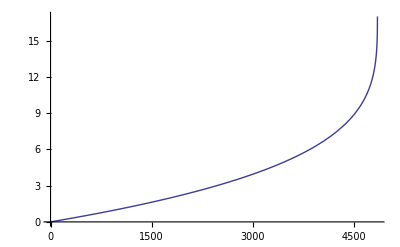

```mathematica
Plot[1/2 (37-√(5+4 √(116281-24 x))),{x,0,4845}]
```

```mathematica
l[0,0,0,0,4,4,0,0]
```

3315

```mathematica
FullSimplify@Solve[l[0,0,0,0,e,f,0,0]==x,f]
```

{{f→1/12 (216-12 e-(8 3^(2/3))/(192150 e-16515 e^2+630 e^3-9 e^4+√3 √(-64+27 ((-35+e) e (610+(-35+e) e)+24 (-969+x))^2)-216 (-969+x))^(1/3)-2 3^(1/3) (192150 e-16515 e^2+630 e^3-9 e^4+√3 √(-64+27 ((-35+e) e (610+(-35+e) e)+24 (-969+x))^2)-216 (-969+x))^(1/3))},{f→1/24 (432-24 e+(16 (-1)^(1/3) 3^(2/3))/(192150 e-16515 e^2+630 e^3-9 e^4+√3 √(-64+27 ((-35+e) e (610+(-35+e) e)+24 (-969+x))^2)-216 (-969+x))^(1/3)+2 3^(1/3) (1-ⅈ √3) (192150 e-16515 e^2+630 e^3-9 e^4+√3 √(-64+27 ((-35+e) e (610+(-35+e) e)+24 (-969+x))^2)-216 (-969+x))^(1/3))},{f→1/24 (432-24 e-(16 (-3)^(2/3))/(192150 e-16515 e^2+630 e^3-9 e^4+√3 √(-64+27 ((-35+e) e (610+(-35+e) e)+24 (-969+x))^2)-216 (-969+x))^(1/3)+2 3^(1/3) (1+ⅈ √3) (192150 e-16515 e^2+630 e^3-9 e^4+√3 √(-64+27 ((-35+e) e (610+(-35+e) e)+24 (-969+x))^2)-216 (-969+x))^(1/3))}}

```mathematica
%/.{e->4.,x->3315}
```

{{f→4.},{f→19.-8.60233 ⅈ},{f→19.+8.60233 ⅈ}}

```mathematica
CForm[18-e-2/(3^(1/3) r)-r/(2 3^(2/3))]
```

18 - e - 2/(Power(3,0.3333333333333333)*r) - r/(2.*Power(3,0.6666666666666666))

```mathematica
CForm[(HornerForm[192150 e-16515 e^2+630 e^3-9 e^4-216 (-969+x)]+√3 √HornerForm[-64+27 ((-35+e) e (610+(-35+e) e)+24 (-969+x))^2])^(1/3)]
```

Power(209304 + e*(192150 + e*(-16515 + (630 - 9*e)*e)) - 216*x + 
    Sqrt(3)*Sqrt(14602721408 + x*(-30139776 + 15552*x) + 
       e*(26811842400 - 27669600*x + e*(10002770460 + 2378160*x + 
             e*(-2027663820 - 90720*x + e*(170362251 + e*(-8089200 + e*(231390 + e*(-3780 + 27*e))) + 1296*x))))),
   0.3333333333333333)

```mathematica
l[0,0,0,0,4,4,4,0]
```

3345

```mathematica
FullSimplify@Solve[l[0,0,0,0,e,f,g,0]==x,g]
```

{{g→1/6 (105-6 e-6 f-√3 √(3675-e (-24814+e (2039+(-74+e) e))+3464 f+12 (-34+e) e f+12 (-17+e) f^2+4 f^3-24 x))},{g→1/6 (105-6 e-6 f+√3 √(3675-e (-24814+e (2039+(-74+e) e))+3464 f+12 (-34+e) e f+12 (-17+e) f^2+4 f^3-24 x))}}

```mathematica
%/.{e->4.,f->4,x->3345}
```

{{g→4.},{g→15.}}

```mathematica
CForm[1/6 (105-6 e-6 f-√3 √(3675-e (-24814+e (2039+(-74+e) e))+3464 f+12 (-34+e) e f+12 (-17+e) f^2+4 f^3-24 x))]
```

(105 - 6*e - 6*f - Sqrt(3)*Sqrt(3675 - e*(-24814 + e*(2039 + (-74 + e)*e)) + 3464*f + 12*(-34 + e)*e*f + 
        12*(-17 + e)*Power(f,2) + 4*Power(f,3) - 24*x))/6.

```mathematica
CForm[1/6 (105-6 e-6 f-Sqrt[HornerForm[3(3675-e (-24814+e (2039+(-74+e) e))+3464 f+12 (-34+e) e f+12 (-17+e) f^2+4 f^3-24 x)]])]
```

(105 - 6*e - 6*f - Sqrt(11025 + f*(10392 + f*(-612 + 12*f)) + 
       e*(74442 + f*(-1224 + 36*f) + e*(-6117 + (222 - 3*e)*e + 36*f)) - 72*x))/6.

```mathematica
FullSimplify@Solve[l[0,0,0,0,e,f,g,h]==x,h]
```

{{h→1/24 (-74 e^3+e^4+e^2 (2051-12 f)+e (-25234-12 (-36+f) f+24 g)-4 (-54 f^2+f^3+f (971-6 g)-3 (-35+g) g-6 x))}}

```mathematica
CForm[HornerForm[(-74 e^3+e^4+e^2 (2051-12 f)+e (-25234-12 (-36+f) f+24 g)-4 (-54 f^2+f^3+f (971-6 g)-3 (-35+g) g-6 x))]/24]
```

(g*(-420 + 12*g) + e*(-25234 + e*(2051 + (-74 + e)*e - 12*f) + (432 - 12*f)*f + 24*g) + 
     f*(-3884 + (216 - 4*f)*f + 24*g) + 24*x)/24.

```mathematica
l[4,0,0,0,0,0,0,0]/4845
```

5781

```mathematica
FullSimplify@Solve[l[a,0,0,0,0,0,0,0]/4845==x,a]
```

{{a→1/2 (45-√(5-4 √(255025-24 x)))},{a→1/2 (45+√(5-4 √(255025-24 x)))},{a→1/2 (45-√(5+4 √(255025-24 x)))},{a→1/2 (45+√(5+4 √(255025-24 x)))}}

```mathematica
opCost[HoldPattern[Plus[l__]]]:=Length[{l}]-1
```

```mathematica
opCost[HoldPattern[Times[l__]]]:=4(Length[{l}]-1)
```

```mathematica
opCost[HoldPattern[Power[l__]]]:=10(Length[{l}]-1)
```

```mathematica
opCost[__]:=0
```

```mathematica
computationCost[compExpr_]:=Module[{accum=0},Scan[accum+=opCost[#]&,compExpr,{0,Infinity}];accum]
```